Find Area of ellipse with this equation using Riemann sum

```mathematica
a = 0
```

0

```mathematica
b = 3
```

3

```mathematica
n = 2000
```

2000

```mathematica
y[x_] := 5(1-(x/3)^2)^(1/2)
```

```mathematica
delta[a_, b_, n_] = (b - a)/n
```

(-a+b)/n

```mathematica
x[a_,b_,n_,i_] := a + i*delta[a,b,n]
```

```mathematica
N[Sum[y[x[a,b,n,i]]*delta[a,b,n],{i,0,n-1}]]
```

11.781

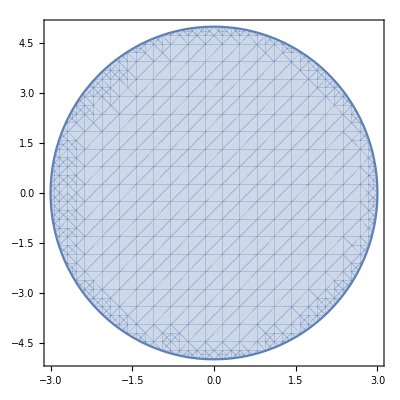

```mathematica
RegionPlot[(x/3)^2+(y/5)^2 <= 1,{x,-3,3},{y,-5,5}]
```